```mathematica
(*Set as ...PathtoGithubFolder/DataFiles *)
dire="~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/WadWan21/";
SetDirectory[dire];
Get[dire<>"/../init.m"]
```

```mathematica
(*Leo T data from Faerman et al. 2013 model*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/LeoT_profiles_Faerman13.dat"];
(*Columns are: r (kpc) n_DM (cm^-3) n_H (cm^-3) n_e (cm^-3) n_HI (cm^-3)*)
data=DeleteDuplicatesBy[data,First];
rl= data[[All,1]];
dml=Interpolation[Transpose[{data[[All,1]],mp/mgev data[[All,2]]}]];
nhl=Interpolation[Transpose[{data[[All,1]],data[[All,3]]}]];
nel=Interpolation[Transpose[{data[[All,1]],data[[All,4]]}]];
nh1l=Interpolation[Transpose[{data[[All,1]],data[[All,5]]}]];
```

InterpolatingFunction::dmval: Input value {0.0000143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

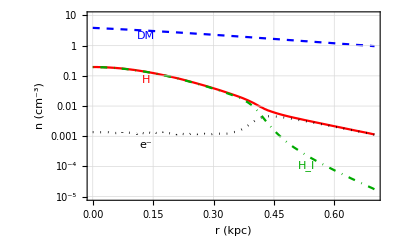

```mathematica
Show[LogPlot[{dml[r],nhl[r],nel[r],nh1l[r]},{r,0,0.7},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.6,FrameLabel->{"r (kpc)","n (cm^-3)"},PlotRange->{{0,0.7},{10^-5,10}},PlotStyle->{{Blue,Dashed},{Red},{Black,Dotted},{Darker[Green],DotDashed},{RGBColor[0.363898, 0.618501, 0.782349],Dashed},{RGBColor[0.647624, 0.37816, 0.614037],DotDashed}}(*PlotRange->{{0.002,10},{4 10^-25,10^-20}},*)],Graphics[{Text[Style["DM",Blue],Scaled[{0.2,0.87}],{0,0},Automatic,{1,0}],Text[Style["H",Red],Scaled[{0.2,0.64}],{0,0},Automatic,{1,0}],Text[Style["e^-",Black],Scaled[{0.2,0.295}],{0,0},Automatic,{1,0}],Text[Style["H_I",Darker[Green]],Scaled[{0.75,0.185}],{0,0},Automatic,{1,0}]}]]
```

## Opacity plots

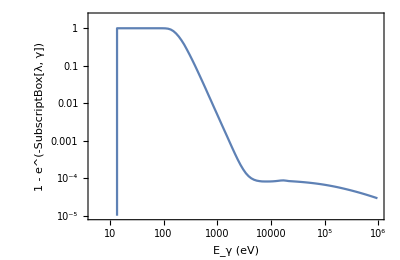

```mathematica
data=Import["PhotonOpacity.dat"];
ListLogLogPlot[data,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400,AspectRatio->0.65,FrameLabel->{Style["E_γ (eV)",18],Style["1 - e^(-SubscriptBox[λ, γ])",20]},PlotRange->{{5,10^6},{10^-5,2}}]
```

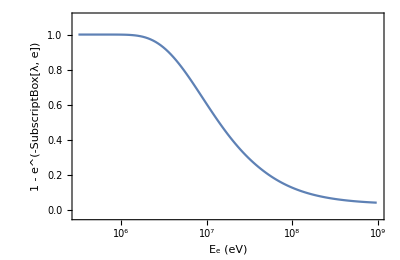

```mathematica
data=Import["ElectronOpacity.dat"];
ListLogLinearPlot[{data},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400,AspectRatio->0.65,FrameTicks->{ {Automatic,Automatic},{ticks,Automatic}},FrameLabel->{Style["E_e (eV)",18],Style["1 - e^(-SubscriptBox[λ, e])",20]},PlotRange->{{10^5.5,10^9},{-0.03,1.1}}]
```

## ALP → γ γ

```mathematica
data0=Import["Axions/LeoT.dat"];
data1=Import["Axions/MWcloud.dat"];
data2={{0.00001182137822475099,1.648533826 10^-16},{0.00001182137822475099 10^10,1.648533826 10^-6}};
data3={{0.01052329872108498, 2.627393166064287 10^-11},{1083.453125076008, 0.0000026434042772659304}};
data4=Import["Axions/BolChl21.dat"];
data5=Import["Axions/Reg21.dat"];
data6=Import["Axions/Gri07.dat"];
data7=Import["Axions/XMM.dat"];
data8=Import["Axions/EBL.dat"];
data9=Import["Axions/x_ion.dat"];
data10=Import["Axions/HorizontalBranch.dat"][[3;;]];
```

```mathematica
(*Producing dashing shown in plots*)
epInt=Interpolation[Transpose[{Log10[data0[[;;,1]]],Log[data0[[;;,2]]]}]];
dashing=Table[{{10.^i,Exp[epInt[i]]},{10.^(i+1),Exp[epInt[i]] 10^10}},{i,1.7,5,0.3}];
dashing=Join[{{{10.^1.45,10^-12},{10.^(1.45+1),10^-2}}},dashing];
```

InterpolatingFunction::dmval: Input value {4.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

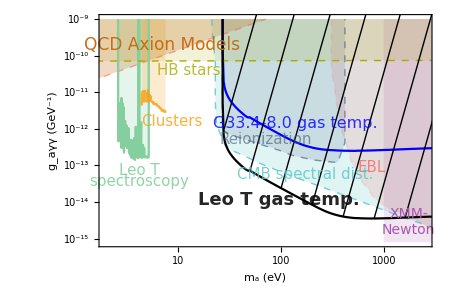

```mathematica
Show[ListLogLogPlot[{data1,data2,data3,data4,data5,data6,data7,data8,data9,data10,data0},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,(*PlotLabel->Style["Decay: χ → γγ",19,Black],*)Filling->{2->{{3},{RGBColor[0.772079, 0.431554, 0.102387, 0.25]}},4->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},5->{Top,RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.2]},6->{Top,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.2]},7->{Top,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},8->{Top,RGBColor[1, Rational[1, 3], Rational[1, 3], 0.14]},9->{Top,RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.15]},10->{Top,RGBColor[Rational[2, 3], Rational[2, 3], 0, 0.15]}},FillingStyle->{Opacity[0.3]},FrameLabel->{Style["m_a (eV)",18],Style["g_aγγ  (GeV^-1)",18]},PlotStyle->{Blue,{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed,Thin},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331]},RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.14],Dashed,Thin},{RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.6],Dashed,Thin},{RGBColor[Rational[2, 3], Rational[2, 3], 0],Dashed,Thin},Black},PlotRange->{{2,2500},{10^-15.1,10^-9}}],Graphics[{Text[Style["QCD Axion Models",RGBColor[0.772079, 0.431554, 0.102387],17],Scaled[{0.19,0.87}],{0,0},{2,0.6}],
Text[Style["Leo T",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.9],15],Scaled[{0.12,0.33}],{0,0},{2,0}],
Text[Style["spectroscopy",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.9],15],Scaled[{0.12,0.28}],{0,0},{2,0}],
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.54,0.20}],{0,0},Automatic,{1,-0.45}],
Text[Style["Clusters",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.22,0.54}],{0,0},{2,0}],
Text[Style["HB stars",RGBColor[Rational[2, 3], Rational[2, 3], 0, 0.8],15],Scaled[{0.27,0.76}],{0,0},{2,0}],
Text[Style["XMM-",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],14],Scaled[{0.93,0.14}],{0,0},{2,0}],
Text[Style["Newton",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],14],Scaled[{0.93,0.07}],{0,0},{2,0}],
Text[Style["EBL",RGBColor[1, Rational[1, 3], Rational[1, 3], 0.7000000000000001],15],Scaled[{0.82,0.34}],{0,0},{1,0}],
Text[Style["CMB spectral dist.",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],15],Scaled[{0.62,0.31}],{0,0},{1,-0.3}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.59,0.53}],{0,0},Automatic,{1,-0.33}],
Text[Style["Reionization",RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667, 0.6],15],Scaled[{0.5,0.46}],{0,0},{1,-0.27}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]]
```

## DM → e^+e^-

```mathematica
data0=Import["ElectronDecay/LeoT.dat"];
data1=Import["ElectronDecay/MWcloud.dat"];
data2=Import["ElectronDecay/CMB.dat"];
data3=Import["ElectronDecay/IGM.dat"];
data4=Import["ElectronDecay/Essig.dat"];
data5=Import["ElectronDecay/Voyager.dat"];
```

```mathematica
epInt=Interpolation[Transpose[{Log10[data0[[All,1]]],Log[data0[[All,2]]]}]];
dashing=Table[{{10.^(i-1),Exp[epInt[i]] 10^-5},{10.^i,Exp[epInt[i]]}},{i,6.5,11,0.8}];
```

InterpolatingFunction::dmval: Input value {9.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

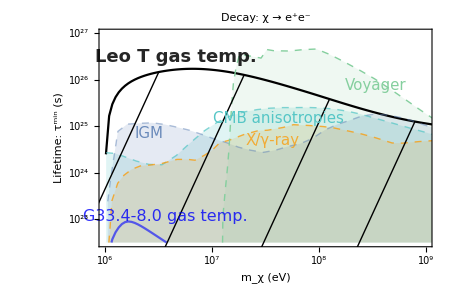

```mathematica
Show[ListLogLogPlot[{data0,data1,data2,data3,data4,data5},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,FrameTicks->{ {"",},{ticks,}},FillingStyle->{Opacity[0.3]}, PlotLabel->Style["Decay: χ → e^+e^-",19,Black],FrameLabel->{Style["m_χ (eV)",18],Style["Lifetime: τ^min (s)",18]},Filling->{3->{Bottom,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},4->{Bottom,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},5->{Bottom,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]},6->{Bottom,RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.13]}},PlotStyle->{Black,RGBColor[0, 0, 1, 0.6],{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.72],Dashed,Thin},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin}},PlotRange->{{10^6,10^9},{10^22.5,10^27.}}],
Graphics[{Text[Style["Voyager",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],15],Scaled[{0.83,0.74}],{0,0},{1,-0.5}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.2,0.14}],{0,0},Automatic,{1,0.}],
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.23,0.87}],{0,0},Automatic,{1,0.}],
Text[Style["X/γ-ray",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.52,0.49}],{0,0},{1,0.15}],Text[Style["CMB anisotropies",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],15],Scaled[{0.54,0.59}],{0,0},{1,0.1}],
Text[Style["IGM",RGBColor[0.368417, 0.506779, 0.709798, 0.91],15],Scaled[{0.15,0.52}],{0,0},{1,0}]}],ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]]
```

## DM DM → e^+e^-

```mathematica
ticks={{10^6,"10^6",{0.01,0}},{10^7,"10^7",{0.01,0}},{10^8,"10^8",{0.01,0}},{10^9,"10^9",{0.01,0}}};
```

```mathematica
data0=Import["ElectronAnnhilation/LeoT.dat"];
data1=Import["ElectronAnnhilation/MWcloud.dat"];
data2=Import["ElectronAnnhilation/Planck.dat"];
data3=Import["ElectronAnnhilation/Integral.dat"];
data4=Import["ElectronAnnhilation/Voyager.dat"];
data5=Import["ElectronAnnhilation/Essig.dat"];
data6=Import["ElectronAnnhilation/Planck_p-wave.dat"];
data7=Import["ElectronAnnhilation/Fermi.dat"];
```

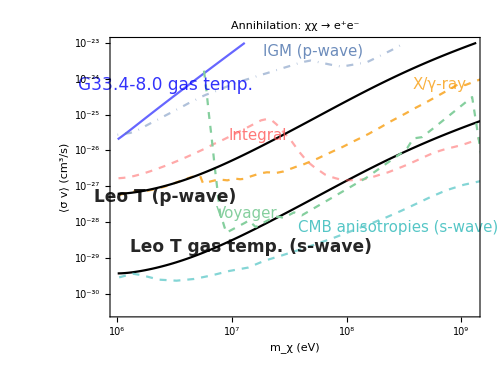

```mathematica
Show[ListLogLogPlot[{data0,data1,data2,data3,data4,data5,data6,Transpose[{data0[[All,1]],data0[[All,2]](220/17)^2}],data7},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->500,AspectRatio->0.75,FrameTicks->{ {"",},{ticks,}},FillingStyle->{Opacity[0.3]}, PlotLabel->Style["Annihilation: χχ → e^+e^-",20,Black],FrameLabel->{Style["m_χ (eV)",20],Style["⟨σ v⟩  (cm^3/s)",20]},PlotStyle->{Black,RGBColor[0, 0, 1, 0.6],{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.72],Dashed},{RGBColor[1, Rational[1, 3], Rational[1, 3], 0.5],Dashed},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],DotDashed},Black,{RGBColor[0.772079, 0.431554, 0.102387, 0.67],Dashed}},PlotRange->{{10^6,10^9.1},{10^-23,10^-30.5}}],
Graphics[{Text[Style["Integral",RGBColor[1, Rational[1, 3], Rational[1, 3], 0.79],15],Scaled[{0.4,0.65}],{0,0},Automatic,{1,0.3}],
Text[Style["Voyager",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],15],Scaled[{0.37,0.37}],{0,0},{1,0.4}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],17],Scaled[{0.15,0.83}],{0,0},Automatic,{1,0.75}],
Text[Style["Leo T gas temp. (s-wave)",GrayLevel[0, 0.85],Bold,17],Scaled[{0.38,0.25}],{0,0},Automatic,{1,0.4}],
Text[Style["Leo T (p-wave)",GrayLevel[0, 0.85],Bold,17],Scaled[{0.15,0.43}],{0,0},Automatic,{1,0.2}],
Text[Style["X/γ-ray",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.89,0.83}],{0,0},{1,0.47}],Text[Style["CMB anisotropies (s-wave)",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9]],15],Scaled[{0.78,0.32}],{0,0},{1,0.4}],
Text[Style["IGM (p-wave)",RGBColor[0.368417, 0.506779, 0.709798, 0.91],15],Scaled[{0.55,0.95}],{0,0},{1,0.1}]}](*,ListLogLogPlot[dashing,Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]*)]
```

## DM -> γγ

```mathematica
LeoTdata=Import["photonDecay/LeoTdata.dat","Data"];
CMBdata=Import["photonDecay/CMBdata.dat","Data"];
Xraydata=Import["photonDecay/Xraydata.dat","Data"];
CMBspecdata=Import["photonDecay/CMBspecdata.dat","Data"];
dDMdata={{1,4.9*10^18},{10^5,4.9*10^18}};
MWdata=Import["photonDecay/MWdata.dat","Data"];
```

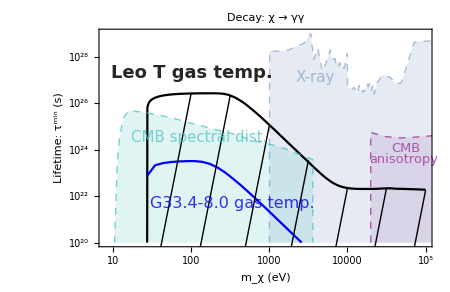

```mathematica
Show[ListLogLogPlot[{LeoTdata,CMBdata,Xraydata,CMBspecdata,dDMdata,MWdata},PlotRange->{{8,10^5},{10^20,10^29}},Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{Style["m_χ (eV)",18],Style["Lifetime: τ^min (s)",18]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,PlotLabel->Style["Decay: χ → γγ",19,Black],
Filling->{2->{Bottom,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},3->{Bottom,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},4->{Bottom,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},5->{Bottom,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]}},FillingStyle->{Opacity[0.3]},PlotStyle->{Black,{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin},Blue}],Graphics[{
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.28,0.8}],{0,0},{2,0}],
Text[Style["CMB",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.92,0.45}],{0,0},{2,0}],
Text[Style["anisotropy",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.915,0.4}],{0,0},{2,0}],
Text[Style["X-ray",RGBColor[0.368417, 0.506779, 0.709798, 0.49],15],Scaled[{0.65,0.78}],{0,0},{2,0}],
(*Text[Style["dDM",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.35,0.08}],{0,0},{2,0}],*)
Text[Style["CMB spectral dist.",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],15],Scaled[{0.3,0.5}],{0,0},{1,-0.25}],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.4,0.2}],{0,0},{1,-0.6}]}],LogLogPlot[10^(17.0096 Log10[x]-7.6),{x,10^1.43,100},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-16.2),{x,10^1.43,10^2.5},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-26),{x,10^1.43,1000},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-36),{x,10^1.43,10^3.5},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-45.7),{x,10^1.43,10000},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-54.2),{x,10^1.43,10^4.5},PlotStyle->{{GrayLevel[0],Thin}}],
LogLogPlot[10^(17.0096 Log10[x]-62.8),{x,10^1.43,10^5},PlotStyle->{{GrayLevel[0],Thin}}]]
```

## CP even scalar

```mathematica
scalarLeoT=Import["scalar/scalarLeoT.dat","Data"];
scalarCMB=Import["scalar/scalarCMB.dat","Data"];
scalarXray=Import["scalar/scalarXray.dat","Data"];
scalarCMBspec=Import["scalar/scalarCMBspec.dat","Data"];
scalarDDM=Import["scalar/scalarDDM.dat","Data"];
scalarStellar1={{100,3.9 10^-6},{101.85,1.26 10^-13},{1102.66,2.87 10^-13},{4331.17,2.07 10^-12},{11.23*1000,8.91 10^-12},{100 1000,10^-10}};
scalarMW=Import["scalar/scalarMW.dat","Data"];
scalarStellar2={{100,4 10^-6},{100 1000,0.0001}};
scalarDashing1={{28,10^-7.7},{100,10^-3.5}};
scalarDashing2={{200,6 10^-10},{1000,10^-3.5}};
scalarDashing3={{2000,3 10^-10},{10000,10^-3.5}};
scalarDashing4={{15000,10^-10},{10^5,10^-3.5}};
```

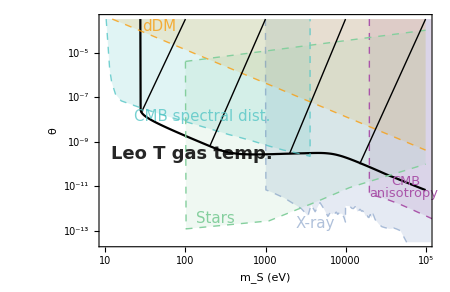

```mathematica
Show[ListLogLogPlot[{scalarLeoT,scalarCMB,scalarXray,scalarCMBspec,scalarDDM,scalarStellar1,scalarStellar2(*,scalarMW*)},Joined->True,PlotRange->{{10,10^5},{10^-3.5,10^-13.5}},Frame->True,FrameStyle->Black,FrameLabel->{Style["m_S (eV)",18],Style["θ",18]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,(*PlotLabel->Style["Decay: χ → νγ",19,Black],*)
Filling->{2->{Top,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},3->{Top,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},4->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},5->{Top,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]},7->{{6},RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331, 0.13]}},FillingStyle->{Opacity[0.3]},PlotStyle->{Black,{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin},{RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],Dashed,Thin}(*,Blue*)}],Graphics[{
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.28,0.4}],{0,0},{1,-0.3}],
Text[Style["CMB",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.92,0.28}],{0,0},{2,0}],
Text[Style["anisotropy",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.915,0.23}],{0,0},{2,0}],
Text[Style["X-ray",RGBColor[0.368417, 0.506779, 0.709798, 0.49],15],Scaled[{0.65,0.1}],{0,0},{2,0}],
Text[Style["dDM",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.18,0.95}],{0,0},{1,-0.35}],
Text[Style["CMB spectral dist.",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],15],Scaled[{0.31,0.56}],{0,0},{1,-0.25}],
Text[Style["Stars",RGBColor[0.5201762735846447, 0.8099999999999999, 0.619472621498331],15],Scaled[{0.35,0.12}],{0,0},{1,0.1}]}],
ListLogLogPlot[{scalarDashing1,scalarDashing2,scalarDashing3,scalarDashing4},Joined->True,PlotStyle->{{GrayLevel[0],Thin}}]]
```

## sterile ν

```mathematica
nuLeoT=Import["nu/nuLeoT.dat","Data"];
nuCMB=Import["nu/nuCMB.dat","Data"];
nuXray=Import["nu/nuXray.dat","Data"];
nuCMBspec=Import["nu/nuCMBspec.dat","Data"];
nuTG={{1,10^-20},{400,10^-20},{400.1,1}};
nuMW=Import["nu/nuMW.dat","Data"];
```

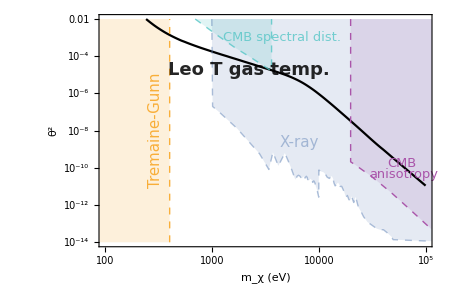

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15,1}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
Show[ListLogLogPlot[{nuLeoT,nuCMB,Join[{{990,0.06}},nuXray,{{2 10^5,10^-14}}],nuCMBspec,nuTG(*,nuMW*)},Joined->True,PlotRange->{{100,10^5},{10^-2,10^-14}},Frame->True,FrameStyle->Black,
FrameTicks->{Automatic,{myTicks,None}},FrameLabel->{Style["m_χ (eV)",18],Style["θ^2",18]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,(*PlotLabel->Style["Decay: χ → νγ",19,Black],*)
Filling->{2->{Top,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},3->{Top,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},4->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]},5->{Top,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]}},FillingStyle->{Opacity[0.3]},PlotStyle->{Black,{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin}(*,Blue*)}],Graphics[{
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,18],Scaled[{0.45,0.76}],{0,0},{1,-0.3}],
Text[Style["CMB",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.91,0.36}],{0,0},{2,0}],
Text[Style["anisotropy",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.915,0.31}],{0,0},{2,0}],
Text[Style["X-ray",RGBColor[0.368417, 0.506779, 0.709798, 0.49],15],Scaled[{0.6,0.45}],{0,0},{2,0}],
Text[Style["CMB spectral dist.",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],13],Scaled[{0.55,0.9}],{0,0},{2,0}],
Text[Style["Tremaine-Gunn",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.17,0.5}],{0,0},{0,1}]}]]
```

## dark neutron

```mathematica
dnLeoT=Import["dark neutron/dnLeoT.dat","Data"];
dnCMB=Import["dark neutron/dnCMB.dat","Data"];
dnDDM=Import["dark neutron/dnDDM.dat","Data"];
dnMW=Import["dark neutron/dnMW.dat","Data"];
dnGamma=Import["dark neutron/dnGamma.dat","Data"];
dnNS={{940,10^-24},{950,10^-23},{950.1,10^-18}};
dnDashing1={{960,10^-17},{950,4 10^-21}};
dnDashing2={{980,10^-17},{970,8 10^-22}};
dnDashing3={{1000,10^-17},{990,4 10^-22}};
dnDashing4={{1020,10^-17},{1010,2.4 10^-22}};
dnDashing5={{1040,10^-17},{1030,1.8 10^-22}};
```

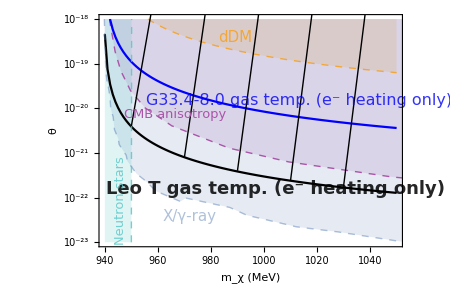

```mathematica
Show[ListLogPlot[{dnLeoT,dnCMB,dnDDM,dnMW,dnGamma,dnNS},Joined->True,PlotRange->{{940,1050},{10^-18,10^-23}},Frame->True,FrameStyle->Black,FrameLabel->{Style["m_χ (MeV)",18],Style["θ",18]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->450,AspectRatio->0.65,(*PlotLabel->Style["Decay: χ → νγ",19,Black],*)
Filling->{2->{Top,RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666, 0.15]},3->{Top,RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.15]},5->{Top,RGBColor[0.368417, 0.506779, 0.709798, 0.16]},6->{Top,RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.18]}},FillingStyle->{Opacity[0.3]},PlotStyle->{Black,{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],Dashed,Thin},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],Dashed,Thin},Blue,{RGBColor[0.368417, 0.506779, 0.709798, 0.49],Dashed,Thin},{RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],Dashed,Thin}}],Graphics[{
Text[Style["Leo T gas temp. (e^- heating only)",GrayLevel[0, 0.85],Bold,18],Scaled[{0.58,0.25}],{0,0},{1,-0.1}],
Text[Style["CMB anisotropy",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],13],Scaled[{0.25,0.57}],{0,0},{1,-0.4}],
Text[Style["dDM",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.45,0.9}],{0,0},{1,-0.2}],
Text[Style["G33.4-8.0 gas temp. (e^- heating only)",RGBColor[0, 0, 0.98, 0.8],16],Scaled[{0.66,0.63}],{0,0},{1,-0.15}],
Text[Style["Neutron stars",RGBColor[Rational[1, 3], Rational[7, 9], Rational[7, 9], 0.8],13],Scaled[{0.07,0.2}],{0,0},{0,1}],
Text[Style["X/γ-ray",RGBColor[0.368417, 0.506779, 0.709798, 0.49],15],Scaled[{0.3,0.13}],{0,0},{1,-0.2}]}],
ListLogPlot[{dnDashing1,dnDashing2,dnDashing3,dnDashing4,dnDashing5},PlotStyle->{{GrayLevel[0],Thin}}]]
```

## DM DM -> γγ

```mathematica
LeoTswave=Import["swave/LeoTswave.dat","Data"];
MWswave=Import["swave/MWswave.dat","Data"];
CMBswave=Import["swave/CMBswave.txt","Data"];
NUSTARswave=Import["swave/NUSTARswave.txt","Data"];
INTEGRALswave=Import["swave/INTEGRALswave.txt","Data"];
```

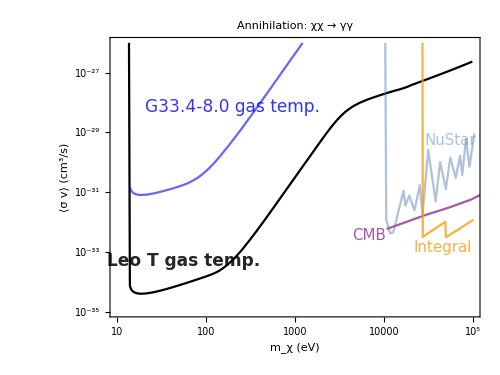

```mathematica
Show[ListLogLogPlot[{LeoTswave,MWswave,CMBswave,NUSTARswave,INTEGRALswave},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->500,AspectRatio->0.75,FillingStyle->{Opacity[0.3]}, PlotLabel->Style["Annihilation: χχ → γγ",20,Black],FrameLabel->{Style["m_χ (eV)",20],Style["⟨σ v⟩  (cm^3/s)",20]},PlotStyle->{Black,RGBColor[0, 0, 1, 0.6],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],{RGBColor[0.368417, 0.506779, 0.709798, 0.49]},{RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81]}},PlotRange->{{10,10^5},{10^-26,10^-35}}],
Graphics[{Text[Style["CMB",RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],15],Scaled[{0.7,0.29}],{0,0},Automatic,{1,0.27}],
Text[Style["NuStar",RGBColor[0.368417, 0.506779, 0.709798, 0.49],15],Scaled[{0.92,0.63}]],
Text[Style["G33.4-8.0 gas temp.",RGBColor[0, 0, 0.98, 0.8],17],Scaled[{0.33,0.75}],{0,0},Automatic,{1,1.3}],
Text[Style["Leo T gas temp.",GrayLevel[0, 0.85],Bold,17],Scaled[{0.2,0.2}],{0,0},Automatic,{1,0.3}],
Text[Style["Integral",RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142, 0.81],15],Scaled[{0.9,0.25}]]}]]
```